```mathematica
kappa:=0.5482;
chip := 1.79285;
gp:=0.27;
Mp:=0.93828;
mpi=0.13957;
gmn[0]:=0.0;
gmn[1]:=0.0;
gmn[2]:=0.0;
gmn[3]:=1.4;
gmn[4]:=1.3;
phi:=0.72;
M2[n_]:=4*kappa^2(n+1/2);
beta[q_,m1_,m2_]:=√(1-2(m1^2+m2^2)/q^2+(m1^2-m2^2)/q^4);
```

```mathematica
gamma[n_,q_,m1_ ,m2_,L_]:=gmn[n] q/(√M2[n])(HeavisideTheta[q^2-(m1+m2)^2]*(beta[q,m1,m2]/beta[√M2[n],m1,m2])^(2L+1));
```

```mathematica
d[q_,n_]:=M2[n]-q^2-I*q*gamma[n,q,mpi,mpi,1];
```

```mathematica
Phi[q_]:=phi*HeavisideTheta[q^2-4*Mp^2];
```

```mathematica
F1p[q_]:=(M2[0]M2[1])/(d[q,0]d[q,1]);
```

```mathematica
F2p[q_]:=chip((1-gp*Exp[I*Phi[q]])(M2[0]M2[1]M2[2])/(d[q,0]d[q,1]d[q,2])+gp*Exp[I*Phi[q]](M2[0]M2[1]M2[2]M2[3]M2[4])/(d[q,0]d[q,1]d[q,2]d[q,3]d[q,4]));
```

```mathematica
GMp[q_]:=F1p[q]+F2p[q];
```

```mathematica
GEp[q_]:=F1p[q]+q^2/(4*Mp^2)F2p[q];
```

```mathematica
Geff[q_]:=√((q^2/(2 Mp^2)(Abs[GMp[q]])^2+(Abs[GEp[q]])^2)/(1+q^2/(2 Mp^2)));
```

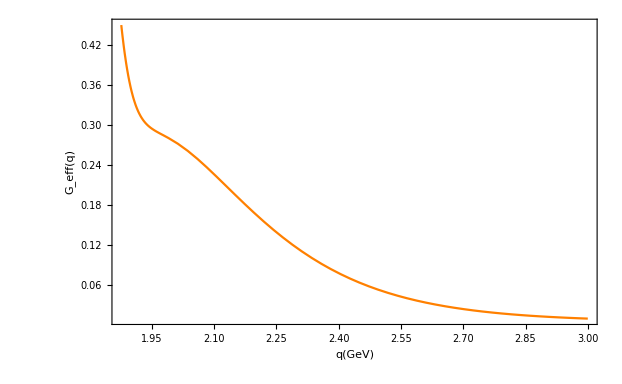

```mathematica
Plot[{Geff[q]},{q,2Mp,3},PlotRange->All,Frame->True,FrameStyle->Directive[Black,20],Axes->False,LabelStyle->Directive[Blue],BaseStyle->{Large,FontFamily->"Courier",FontSize->12},PlotStyle-> {Blue,Orange},FrameLabel->{"q(GeV)","G_eff(q)"}]
```

```mathematica
gmn[0]:=0.149;
gmn[1]:=0.4;
gmn[2]:=0.25;
```

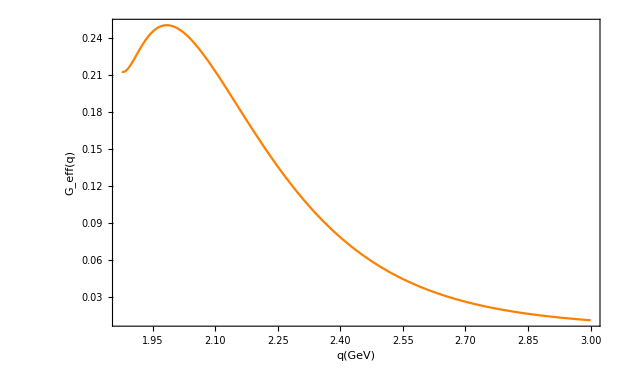

```mathematica
Plot[{Geff[q]},{q,2Mp,3},PlotRange->All,Frame->True,FrameStyle->Directive[Black,20],Axes->False,LabelStyle->Directive[Blue],BaseStyle->{Large,FontFamily->"Courier",FontSize->12},PlotStyle-> {Blue,Orange},FrameLabel->{"q(GeV)","G_eff(q)"}]
```